# Emoji Generation From Singular 2D Images

Parth Kashikar

Giulio Alessandrini

## Introduction

The aim of this project is to create an algorithm for generating semantically and chromatically similar looking Emojis [avatars] from faces of human beings. This has been achieved by a combination of deep learning and heuristic analysis to produce appropriate results.  The datasets used in this project are available for public use and have been referenced below. This report has been divided into two major sections, namely - human analysis and emoji segmentation. Finally, a mapping function is presented to generate the final results.  The key principle involved in achieving the goal is cross-domain semantic preservation for effective results.

## Human Domain

### Face/Hair Segmentation mask generation

One of the key features of a human face to keep in mind is the shape of the hair. For effectively extracting the hair out of a given picture, an edited version of the Dilated ResNet-105 has been trained on a dataset containing face/hair masks of faces from the CelebA dataset. The changes made in the network are for incorporating the training of appropriate dimensions of input and target vectors.

```mathematica
net = NetModel["Dilated ResNet-105 Trained on Cityscapes Data"];
netReplaced = NetReplacePart[net, "input_0"-> NetEncoder[{"Image",{178,218}}]];
netPart=NetTake[netReplaced,{All,"broadcast_add0"}];
newNet =NetGraph[{netPart, DeconvolutionLayer[3,{24,28},"Stride"-> {6,9}, "PaddingSize"-> {{4,4},{4,4}},"Input" -> {19,28,23}],TransposeLayer[{1<->3,1<->2}],SoftmaxLayer[]},{1->2,2->3,3->4}]
```

This network is trained to classify every pixel of any input image into one of three classes, each of those classes corresponding to one color of the segmentation mask [face, hair or background]. The loss function utilized is the “CrossEntropyLossLayer” function.  It has been trained on the 3500 pictures using  cross validation techniques over 10 epochs with a batch size of 4 images, due to the relatively small number of training samples available for the task.

-Graphics- → -Graphics-  [A typical sample from the training data]

Output generator for arbitrary input image:

```mathematica
net = Import[FileNameJoin[{NotebookDirectory[],"mynet.wlnet"}]];
GetHairMaskPerson[Img_]:=Module[{i = Img,image,m},
i = ImageResize[i, {178,218}];
image = net[i];
m = ColorNegate[Binarize[ColorDistance[ImageResize[Image[Round[image]],{178,218}],Red]]]
]
```

```mathematica
GetHairMaskPerson[-Graphics-]
```

-Graphics-

### Color Preservation for translation to Emoji

For color extraction of the various facial features for a given input image, the approach adopted is face-point based analysis predicted using the “2D Face Alignment” network from the Wolfram Neural Network Repository. WIth some simple rules established with respect to the morphological components of the face, we are easily able to extract the skin, hair and iris colors of an arbitrary input.

#### 2 D Face Alignment Neural Network

```mathematica
netevaluation[image1_]:=Block[{heatmaps,posFlattened,posMat},heatmaps=NetModel["2D Face Alignment Net Trained on 300W Large Pose Data"][image1];
posFlattened=Map[First@Ordering[#,-1]&,Flatten[heatmaps,{{1},{2,3}}]];
posMat=QuotientRemainder[posFlattened-1,64]+1;
1/64.*Map[{#[[2]],64-#[[1]]+1}-0.5&,posMat]];
groupings=Span@@@{{1,17},{18,22},{23,27},{28,36},{37,42},{43,48},{49,60},{61,68}};
```

```mathematica
landmarks=netevaluation[-Graphics-];
HighlightImage[-Graphics-,Graphics@Riffle[Thread@Hue[Range[8]/8.],Map[Point,Part[landmarks,#]&/@groupings]],DataRange->{{0,1},{0,1}},ImageSize->300]
```

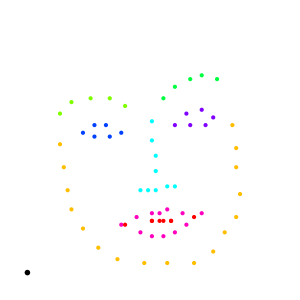

#### Helper Functions for picking out various useful colors

```mathematica
PickSkinColorPerson[img_]:=Module[{image = img,landmarks,splits,vals,mean},
landmarks=netevaluation[image];
splits = landmarks[[#]]&/@groupings;
vals = PixelValue[image,#]&/@ScalingTransform[ImageDimensions[image]]@splits[[4]];
mean = Mean[vals[[1;;4]]];
RGBColor[mean]]
```

```mathematica
PickSkinColorPerson[-Graphics-]
```

RGBColor[{0.9098039215686274, 0.7892156862745099, 0.7186274509803922, 1.}]

```mathematica
PickHairColorPerson[img_]:=Module[{image=img,net,i,m},net=Import["/home/kashikar/trained.mx"];
i=ImageResize[image,{178,218}];
image=net[i];
m=ColorNegate[Binarize[ColorDistance[ImageResize[Image[Round[image]],{178,218}],Red]]];
DominantColors[i,Masking->m][[1]]]
```

```mathematica
PickHairColorPerson[-Graphics-]
```

RGBColor[0.023076545055337665, 0.012205095915480992, 0.015057438223672647]

```mathematica
PickIrisColorPerson[img_]:=Module[{image = img,landmarks,splits,poly,eyecolors,skin,eyecolor},

landmarks=netevaluation[image];
splits = landmarks[[#]]&/@groupings;
poly = Polygon[ScalingTransform[ImageDimensions[image]]@splits[[5]]];
eyecolors = DominantColors[image, Masking -> poly];
skin = PickSkinColorPerson[image];
eyecolor = Select[eyecolors,Function[ColorDistance[#,White]>0.2&&ColorDistance[#,skin]>0.2&&ColorDistance[#,Black]>0.2]][[1]]]
```

```mathematica
PickIrisColorPerson[-Graphics-]
```

RGBColor[0.28888057556290486, 0.29376721614167123, 0.3207488974600684, 1.]

## Emoji Domain

### Structural Extraction and Analysis

The dataset we use for the making avatars is the CartoonSet compilation of images wherein a certain number of hairstyles, jawline types, and eye variations have been procedurally combined to create 100k avatars. It should be noted here that the nose and mouth of every emoji are in them same coordinates, with variance in jawlines and appropriate hairstyles.

```mathematica
-Graphics-,-Graphics-,-Graphics-,-Graphics-
```

Considering we have hair masks for faces, a heuristic can be setup based on masking specific regions of any arbitrary emoji, taking advantage of the common positions in the dataset, to extract hair, and corresponding jawline/ear combinations for the input.

```mathematica
ExtractHairEmoji[img_]:=Module[{image = img,image1,poly,skin,cols,haircolor},
image1 = RemoveAlphaChannel[image,White];
poly = ;
skin =RGBColor[ PixelValue[image, {{247,197}}][[1]]];
cols = DominantColors[image1, Masking -> poly];
haircolor = SelectFirst[cols, ColorDistance[#,White]>0.001 && ColorDistance[#,skin]>0.001&];
FillingTransform[SelectComponents[Binarize[ImageAdjust[ColorDistance[image,haircolor]],{0,0.1}],"Count",-1]]]
```

```mathematica
ExtractHairEmoji[-Graphics-]
```

-Graphics-

Similarly, we can also extract jawlines and ear combinations, which could be potentially used for better fitting of face to emoji contours. It must be noted that this works on region based color distance mapping, and hence doesn’t necessarily return the required outputs.

```mathematica
ExtractJawlineEmoji[Image_]:=Module[{image = Image,poly,skin,cols,haircolor,refRectJawline,refRectleftEar,refRectRightEar,bb,regions,areavals,bigindexjaw,bigindexle,bigindexre}, 

image = RemoveAlphaChannel[image,White];
 poly = ; 
 skin =RGBColor[ PixelValue[image, {{247,197}}][[1]]];
 cols = DominantColors[image, Masking -> poly];
 haircolor = SelectFirst[cols, ColorDistance[#,White]>0.001 && ColorDistance[#,skin]>0.001&];
 refRectJawline = Rectangle[{167.,117.},{332.,225.}];
 refRectleftEar = Rectangle[{138.,188.},{168.,251.}];
 refRectRightEar = Rectangle[{328.,188.},{361.,250.}];
 poly = ;
 cols = DominantColors[image,Masking->poly];

      If[Not[AnyTrue[cols,ColorDistance[#,haircolor]<0.02&]]&&ColorDistance[haircolor,Black]>0.2,{bin = Binarize[ImageAdjust[ColorDistance[image,Black]],{0,0.1}];
	bb = ComponentMeasurements[bin,"BoundingBox"];
	regions = Rectangle[bb[[#]][[2]][[1]],bb[[#]][[2]][[2]]]&/@Range[Length[bb]];
	areavals =Area[RegionIntersection[#,refRectJawline]]&/@regions/. Undefined -> 0;
	bigindexjaw = Ordering[areavals][[-1]];
	areavals =Area[RegionIntersection[#,refRectleftEar]]&/@regions/. Undefined -> 0;
	bigindexle = Ordering[areavals][[-1]];
	areavals =Area[RegionIntersection[#,refRectRightEar]]&/@regions/. Undefined -> 0;
	bigindexre = Ordering[areavals][[-1]];
	SelectComponents[bin,MemberQ[ bb[[{bigindexjaw},2]],#BoundingBox] &],SelectComponents[bin,MemberQ[ bb[[{bigindexjaw,bigindexle,bigindexre},2]],#BoundingBox] &],image = RemoveAlphaChannel[image,White];
	poly = ;
	skin =RGBColor[ PixelValue[image, {{247,197}}][[1]]];
	cols = DominantColors[image, Masking -> poly];
	haircolor = SelectFirst[cols, ColorDistance[#,White]>0.001 && ColorDistance[#,skin]>0.001&];
FillingTransform[SelectComponents[Binarize[ImageAdjust[ColorDistance[image,haircolor]],{0,0.1}],"Count",-1]]},"Null"]]
```

```mathematica
ExtractJawlineEmoji[-Graphics-]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

#### Helper Functions for color extraction

```mathematica
Eyebrowcoloremoji[Image_,color_]:= Module[{img = Image,mask,cols},
mask = ;
cols = DominantColors[img, Masking->mask];
NearestTo[color][cols]]
```

```mathematica
Eyebrowcoloremoji[-Graphics-,HairColorEmoji[-Graphics-]]
```

{RGBColor[0.5184193329836375, 0.2010617900893898, 0.11457775040140408, 1.]}

```mathematica
SkinColorEmoji[Image_]:=Module[{img = Image,skin},
skin =RGBColor[ PixelValue[img, {{247,197}}][[1]]]]

SkinColorEmoji[-Graphics-]
```

RGBColor[{0.6666666666666666, 0.4549019607843137, 0.32941176470588235, 1.}]

```mathematica
HairColorEmoji[Img_]:=Module[{image = Img,expt1,poly,skin,cols,},
expt1 = RemoveAlphaChannel[image,White];
poly = ;
skin =RGBColor[ PixelValue[image, {{247,197}}][[1]]];
cols = DominantColors[expt1, Masking -> poly];
haircolor = SelectFirst[cols, ColorDistance[#,White]>0.001 && ColorDistance[#,skin]>0.001&]]
```

```mathematica
HairColorEmoji[-Graphics-]
```

RGBColor[0.8472878418224745, 0.6041864384284773, 0.19683189824028047]

### Data Processing

The next steps involved are to create chunks of associations labelling emoji segmentation masks with their names, and more importantly, generating a final list with unique hairstyles that conform to the heuristics involved in the generating process.

```mathematica
dir = {"/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/animated/cartoonset100k/0/","/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/animated/cartoonset100k/1/"};
imageFiles=FileNames["/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/animated/cartoonset100k/*/*.png"];
chunks=Partition[imageFiles,1000][[78;;]];
Table[
Export[
FileNameJoin[{"/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/chunks",CreateUUID[]<>".mx"}],
DeleteCases[AssociationMap[ExtractJawline[Import[#]]&,chunk],Null]
],

{chunk,chunks}]
implistchunkdir[n_]:=Module[{num = n,chunkdir, listchunkdir},
chunkdir = "/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/chunks/";
listchunkdir=FileNames["*",chunkdir];
Import[listchunkdir[[num]]]]

getminiruleslist[Dat_]:= Module[{data = Dat,test,groups},
groups=Gather[Normal@data,ImageDistance[#1[[2,3]],#2[[2,3]]]<40&];
test = groups[[All,1]];
DeleteCases[ test, _ -> {_,_,-Graphics-}]
]
$HistoryLength=0;
Export["collection"<>ToString[#]<>".mx",getminiruleslist[implistchunkdir[#]]];&/@Range[4,100]
dircoll = "/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/collections/";
names = FileNames[“*”, dircoll];
final = Cases[Import[names[[1]]], Verbatim[Rule][_String,{Repeated[_Image,{3}]}]];
Length[final]
101
AppendTo[final, Cases[Import[names[[2]]], Verbatim[Rule][_String,{Repeated[_Image,{3}]}]]]&/@Range[2,100];
Length[Flatten[final]]
9308
final = Flatten[final];
absfinal = getminiruleslist[f];
Length[absfinal]
423
Export["/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/absfinal.mx",absfinal];
```

This has been followed by a manual intervention over the remaining 423 images to remove edge cases such as beards, spectacles and other similar outlier combinations. The end file is saved as “useful.mx” and used for future fitting purposes.

```mathematica
Import["/home/kashikar/useful.mx"][[1;;3]]
```

{/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/animated/cartoonset100k/8/cs835724139564498186.png→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/animated/cartoonset100k/8/cs8357809746135659915.png→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/animated/cartoonset100k/8/cs8359216159946317548.png→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

## Mapping

Now that we have extracted all the required data for mapping, we utilize Wolfram Language’s  ImageCrop function to create a function to calculate the percentage overlap mapped over the curated unique emoji list and return the filename of the emoji with the best fitting skeleton. The hairlist variable has been made global to avoid re-importing of the data for faster emojification.

```mathematica
hairlist=;
SelectFitter[Image_]:=Module[{image=Image,nf,hairmask,emojifile,pics,l1,num},
hairmask=GetHairMaskPerson[image];
pics=ImageResize[#,{178,218}]&/@hairlist[[All,2,3]];
l1=Divide[Total[Flatten[ImageData[Abs[ImageCrop[#]-ImageResize[ImageCrop[Binarize[ImageAlign[#,hairmask]]],ImageCrop[#]//ImageDimensions]]]]],2*Times@@ImageDimensions@ImageCrop@#]&/@pics;
num=Position[l1,Min[l1]][[1]];
hairlist[[num,1]]]
```

```mathematica
SelectFitter[-Graphics-]
```

```mathematica
{"/home/kashikar/Drive/AI/Wolfram/Wolfram Summer School/animated/cartoonset100k/8/cs8380910194137324891.png"}
```

```mathematica
Import[%[[1]]]
```

-Graphics-

And finally,  we colorize this skeleton emoji appropriately!

```mathematica
Emoji[Image_]:= Module[{img = Image,eyecolperson,haircolperson,skincolperson,emojistd,skincolemoji,eyecolemoji,emojichanged,hairmask},
eyecolperson = PickIrisColorPerson[img];
haircolperson = PickHairColorPerson[img];
skincolperson = PickSkinColorPerson[img];
emojistd = Import[SelectFitter[img][[1]]];
skincolemoji = SkinColorEmoji[emojistd];
eyecolemoji = DominantColors[emojistd,Masking->][[1]];
emojichanged = ColorReplace[emojistd,{skincolemoji -> skincolperson,eyecolemoji->eyecolperson},{0.1,0.1}];
hairmask = ExtractHairEmoji[emojistd];
emojichanged = ImageResize[ImageApply[#-# + {haircolperson[[1]],haircolperson[[2]],haircolperson[[3]],1}&,emojichanged,Masking->hairmask], 300]]
```

```mathematica
Emoji[-Graphics-]
```

-Graphics-

## Results

Face-Fitting Display

HighlightImage[ImageCrop[ImageResize[ExtractHairEmoji[Import[SelectFitter[-Graphics-][[1]]]],{178,218}]],ImageResize[ImageCrop[ImageAlign[ImageResize[ExtractHairEmoji[Import[SelectFitter[][[1]]]],{178,218}],GetHairMaskPerson[]]],ImageDimensions[ImageCrop[ImageResize[ExtractHairEmoji[Import[SelectFitter[][[1]]]],{178,218}]]]]]
-Graphics- , -Graphics-

## Future Improvements:

Integration of some functions to map hairstyles and jawlines together, varying the hairstyle according to the jawline chosen.

Spectacle detection and improvement of the hair/face segmentation dataset for inclusion of a wider variety of hair.

Improving upon the SelectFitter function for a better metric of contour-shape similarity.

Curating a dataset with pre-decided anchor points of the graphics to manipulate the required semantic features, and clearer coloring.